# Moments

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
datahA={};
datawAX={};
databX={};
Do[

AppendTo[datahA,Import["../data_learned/moments/hA_"<>IntegerString[iOpt,10,3]<>".txt","Table"][[1]]];

AppendTo[datawAX,Import["../data_learned/moments/wAX_"<>IntegerString[iOpt,10,3]<>".txt","Table"][[1]]];

AppendTo[databX,Import["../data_learned/moments/bX_"<>IntegerString[iOpt,10,3]<>".txt","Table"][[1]]];
,{iOpt,1,999,1}]
```

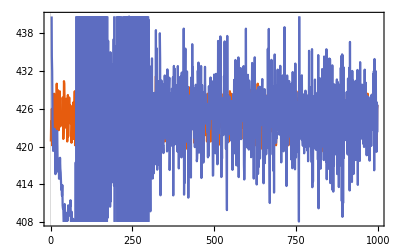
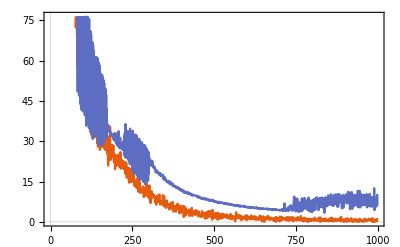
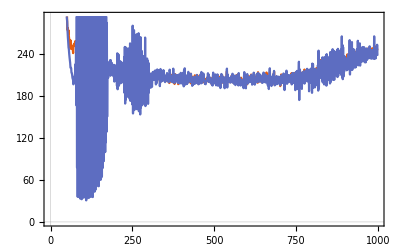

```mathematica
Row[{
ListLinePlot[Transpose[datahA]],
ListLinePlot[Transpose[datawAX]],
ListLinePlot[Transpose[databX]]
}]
```